```mathematica
kC = 3 * 10^10;
kR = 83144626.1815324;            
kHplank = 6.62 * 10^-27;
kb = 1.3807 * 10^-16;
kSt = 6.65210 * 10^-25; 
 kMhydrogen = 1.6735575 * 10^-24;
kStefanBoltzmann = 5.670374419 * 10^-5; 
eV=241799050402417.;
A=(2 kb^4)/(kC^2 kHplank^3);
f[x_]:=NIntegrate[t^3/(Exp[t]-1),{t,0,x}]
f0[x_]:= Piecewise[{{x^3(1/3-x/8+x^2/62.4),x≤2},{Pi^4/15-Exp[-x](x^3+3 x^2+6x+7.28),x>2}}]
```

0.00762079

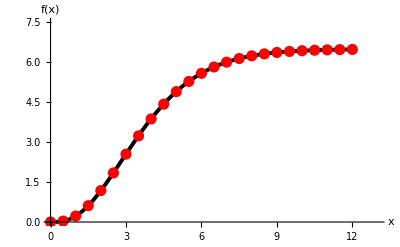

```mathematica
Max[Table[Abs[f[x]-f0[x]],{x,3,5,0.01}]]
F=Table[{x,f0[x]},{x,0,12,0.5}];
Show[Plot[f[x],{x,0,12}, PlotRange->{{0,13},{0,Pi^4/15+1}},PlotStyle->Directive[Black,Thickness[0.007]],AxesStyle->Directive[Black, 17,Arrowheads[.04]],
AxesLabel->{"x","f(x)"}], ListPlot[F, PlotStyle->Directive[Red, PointSize[0.02]]]]
```

```mathematica
T=27.282;
v1=10^17;
v0=0;
A*(f0[ (kHplank v1)/(kb T)]-f0[(kHplank v0)/(kb T)])T^4
kStefanBoltzmann/Pi T^4
```

General::munfl: Exp[-175745.] is too small to represent as a normalized machine number; precision may be lost.

10.0144

9.99923

```mathematica
R=0.3;
U[r_,kin_,kout_, Q_]:=Q Piecewise[{{1/2 NIntegrate[(1-Exp[-kin(2 √(R^2-r^2(1-μ^2)))])Exp[-kout(r μ-√(R^2-r^2(1-μ^2)))],{μ,√(1-(R/r)^2),1}],r≥R},{NIntegrate[1-Cosh[kin r μ]Exp[-kin √(R^2-r^2(1-μ^2))],{μ,0,1}],r<R}}]
X=Table[i,{i,0,1,0.01}];
{kC/(100*10^-7),kC/(800*10^-7), (kC/(100*10^-7)-kC/(800*10^-7))/20.}//N;
V=Table[v,{v,3.33*10^14,3.*10^15,(kC/(100*10^-7)-kC/(800*10^-7))/50.}];

Ie[T_,v1_,v0_]:=A*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4
absorp[d_,T_,v1_,v0_]:=d/(4 A*Pi*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4)
```

```mathematica
sol=Table[{V[[i]],U[R,absorp[10^-4,1000,V[[i+1]],V[[i]]],absorp[10^-100,1000,V[[i+1]],V[[i]]], Ie[1000,V[[i+1]],V[[i]]]]}, {i,1,Length[V]-1}];
```

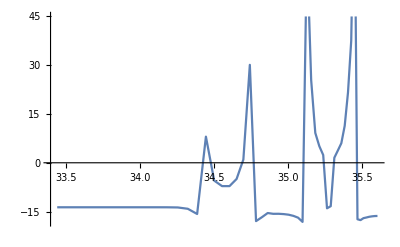

```mathematica
ListLinePlot[Log@sol]
```

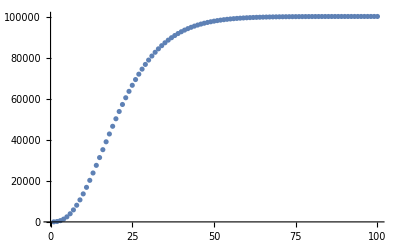

```mathematica
ListPlot[Table[Ie[273,x,0],{x,10^12,10^14,10^12}],PlotRange->All]
```

```mathematica
T=27.282;
v1=3*10^17;
v0=10^17;
Ie[T,v1,v0]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

-10.0144

```mathematica
q[x_]:=x^3+3 x^2+6x+7.28
IeLog[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)]q[V0]-Exp[-AA/2(V1-V0)]q[V1]]
```

```mathematica
IeLog[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-175745.] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
IeLog2[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)+Log[q[V0]]]-Exp[-AA/2(V1-V0)+Log[q[V1]]]]
IeLog2[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-175624.] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
IeLog3[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)-AA/4(V1-V0)+Log[Exp[3/2 AA/2(V1-V0)+Log[q[V0]]]-Exp[-1/2 AA/2(V1-V0)+Log[q[V1]]]]
IeLog3[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-87751.7] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
3/2(kHplank/(kb T))/2(v1-v0)+Log[q[v0]]
```

263735.

```mathematica
q0[x_]:=x^3(1/3-x/8+x^2/62.4)
IeLog5[AA_,V0_,V1_]:= 
Piecewise[{{Log[A*(q0[AA*V1]-q0[AA*V0])],AA*V1≤2},{Piecewise[{{ Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)]q[V0]-Exp[-AA/2(V1-V0)]q[V1]],AA/2(V1-V0)<700},{Log[A]-AA/2(V0+V1)+AA/2(V1-V0)+Log[q[V0]],AA/2(V1-V0)>=700}}],AA*V1>2}}]
```

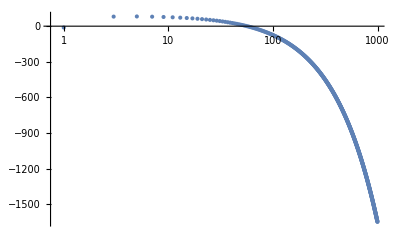

```mathematica
ListLogLinearPlot[Table[{x/10^14,Re@IeLog5[kHplank/(kb T*100),x-2*10^14,x]},{x,10^14,10^17,2*10^14}],PlotRange->All]
```

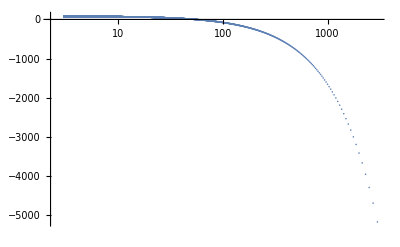

```mathematica
ListLogLinearPlot[Table[{(kC/λ)/10^14,IeLog5[kHplank/(kb T*100),kC/λ,kC/(λ-0.999*10^-7)]},{λ,1000*10^-7,0.1*10^-7,-0.1*10^-7}],PlotRange->All]
```

```mathematica
kStefanBoltzmann*T^4/Pi
Ie[T,10^14,0]
Exp[IeLog5[kHplank/(kb T),0,10^14]+4Log[T]]
```

9.99923

10.0144

11.2266

```mathematica
(*Ie[T_,v1_,v0_]:=A*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4*)
IeExp[AA_,V0_,V1_]:= A(Exp[-AA V0]q[V0]-Exp[-AA(V1)]q[V1])
IeExp[kHplank/(kb T),0,10^14]*T^4
Exp@IeLog5[kHplank/(kb T),0,10^20]*T^4
```

11.2266

11.2266

```mathematica
Table[x/10^14,{x,10^14,10^17,2*10^14}]//N ;
Table[λ,{λ,1000*10^-7,3*10^-7,-1*10^-7}]//N;
```

^2

```mathematica
Pi^4/15-q0[2]
```

5.31445

```mathematica
Pi^4/15-Exp[-2]*q[2]
```

1.17797

```mathematica
Log[5]//N
```

1.60944

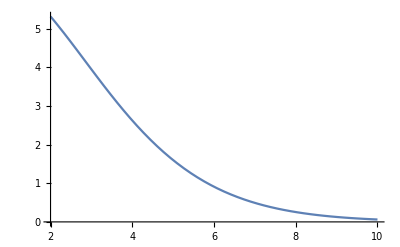

```mathematica
Plot[Exp[-x]*q[x],{x,2,10}]
```

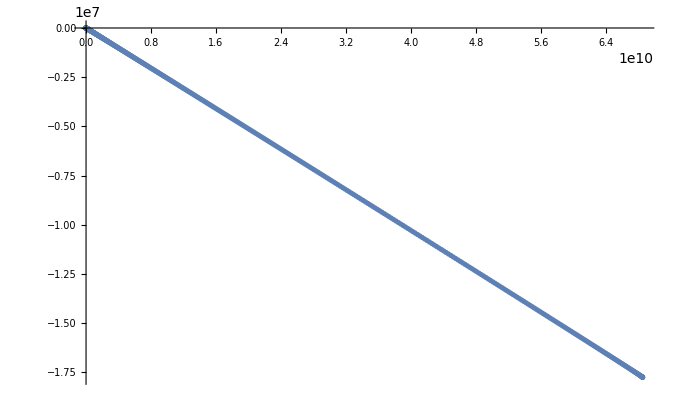

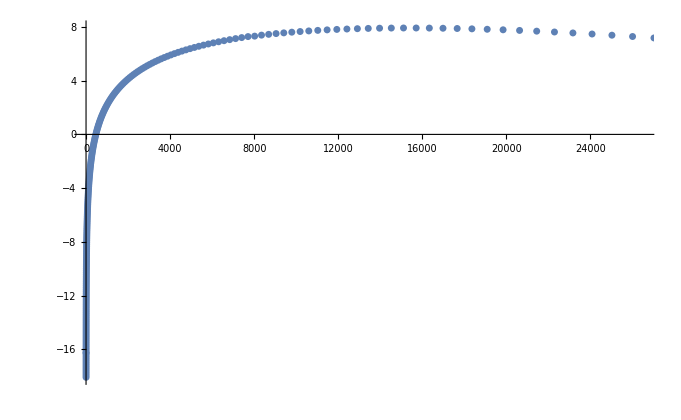

{{11.4158,-10.9855},{10.8865,-11.1268},{10.3812,-11.2684},{9.89891,-11.4101},{9.43853,-11.5519},{8.9991,-11.6939},{8.57971,-11.836},{8.17945,-11.9783},{7.79748,-12.1208},{7.43297,-12.2634},{7.08514,-12.4062},{6.75326,-12.5491},{6.4366,-12.6922},{6.13448,-12.8354},{5.84625,-12.9787},{5.57128,-13.1223},{5.30898,-13.266},{5.05878,-13.4098},{4.82013,-13.5538},{4.5925,-13.6979},{4.37541,-13.8422},{4.16837,-13.9866},{3.97093,-14.1312},{3.78265,-14.276},{3.60312,-14.4209},{3.43194,-14.5659},{3.26872,-14.7111},{3.11312,-14.8565},{2.96477,-15.002},{2.82335,-15.1476},{2.68854,-15.2934},{2.56005,-15.4394},{2.43757,-15.5855},{2.32083,-15.7318},{2.20957,-15.8782},{2.10355,-16.0248},{2.00251,-16.1715},{1.90623,-16.3184},{1.81448,-16.4654},{1.72707,-16.6126},{1.64378,-16.7599},{1.56444,-16.9074},{1.48884,-17.055},{1.41683,-17.2028},{1.34824,-17.3507},{1.2829,-17.4988},{1.22067,-17.647},{1.1614,-17.7954},{1.10495,-17.944},{1.05119,-18.0926},{0,-16.2698}}

General::munfl: Exp[-1.77575×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.77562×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.7754×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

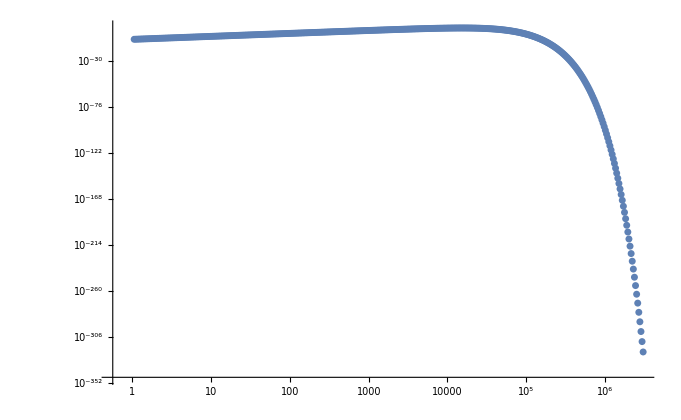

```mathematica
(*C++ расчёт*)
fplank=Import["/home/artem/projects/test/plank.txt","table"];
fplankL=Import["/home/artem/projects/test/plankL.txt","table"];
ListPlot[{fplank}]
ListPlot[Table[fplank[[i]],{i,750,Length@fplank}]]
Table[fplank[[i]],{i,950,Length@fplank}]
ListLogLogPlot[Table[{fplank[[i,1]],Exp@fplank[[i,2]]},{i,1,Length@fplank}]]
```

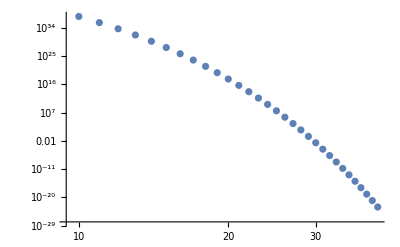

```mathematica
tem=10^4;
(*int[x,Inf]{sigmaT^4}*)
ListLogLogPlot[Table[{x/10^15,Exp[Re@IeLog5[kHplank/(kb tem),x,10^20]+4Log[tem]]},{x,10^16,4*10^16,10^15}],PlotRange->All]
```

```mathematica
(10^20-10^11)/1000//N
```

1.×10^17

-Graphics-

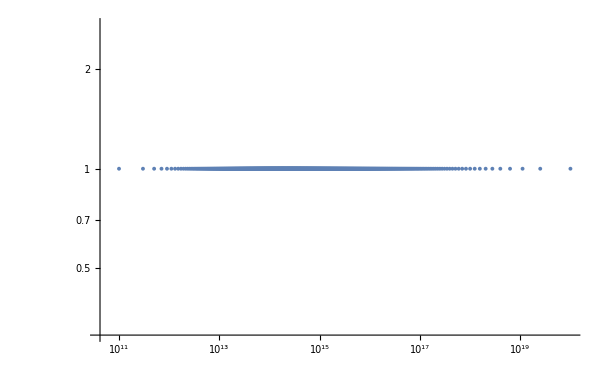

```mathematica
FF[x_]:=a 1/x^2+c
ans=NSolve[{FF[1]==10^20,FF[1000]==10^11},{a,c},Reals][[1]];
ListPlot[Table[{x,FF[x]/.ans},{x,1,1000}],PlotRange->All]
ListLogLogPlot[Table[{FF[x]/.ans,1},{x,1,1000}],PlotRange->All]
```

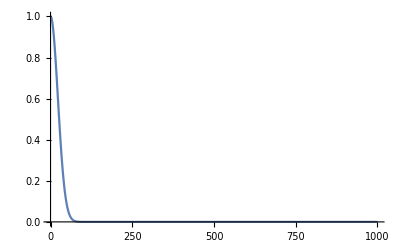

1.38879×10^-11

```mathematica
Plot[(a Exp[-x^2/b]+c)/.{a->1,b->1000,c->0},{x,0,1000},PlotRange->All]
(a Exp[-x^2/b]+c)/.{a->1,b->40000,c->0,x->1000}//N
```

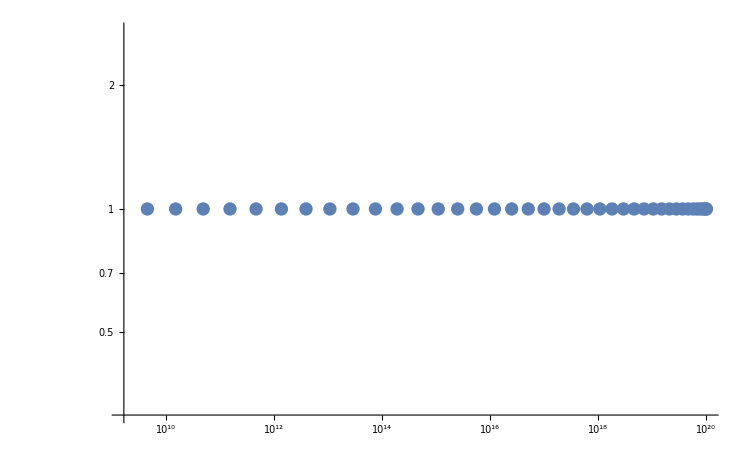

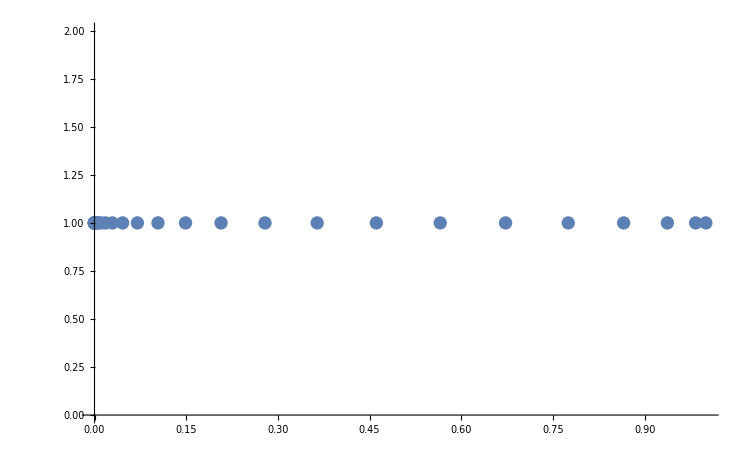

{{9.99978×10^19,1.},{9.99911×10^19,1.},{9.998×10^19,1.},{9.99645×10^19,1.},{9.99445×10^19,1.},{9.992×10^19,1.},{9.98912×10^19,1.},{9.98579×10^19,1.},{9.98202×10^19,1.},{9.9778×10^19,1.},{9.97315×10^19,1.},{9.96805×10^19,1.},{9.96251×10^19,1.},{9.95654×10^19,1.},{9.95012×10^19,1.},{9.94327×10^19,1.},{9.93598×10^19,1.},{9.92826×10^19,1.},{9.9201×10^19,1.},{9.91151×10^19,1.},{9.90248×10^19,1.},{9.89302×10^19,1.},{9.88313×10^19,1.},{9.87282×10^19,1.},{9.86207×10^19,1.},{9.8509×10^19,1.},{9.83931×10^19,1.},{9.82729×10^19,1.},{9.81485×10^19,1.},{9.80199×10^19,1.},{9.78871×10^19,1.},{9.77501×10^19,1.},{9.7609×10^19,1.},{9.74638×10^19,1.},{9.73145×10^19,1.},{9.71611×10^19,1.},{9.70036×10^19,1.},{9.6842×10^19,1.},{9.66765×10^19,1.},{9.65069×10^19,1.},{9.63334×10^19,1.},{9.61558×10^19,1.},{9.59744×10^19,1.},{9.5789×10^19,1.},{9.55997×10^19,1.},{9.54066×10^19,1.},{9.52096×10^19,1.},{9.50089×10^19,1.},{9.48043×10^19,1.},{9.45959×10^19,1.},{9.43839×10^19,1.},{9.41681×10^19,1.},{9.39486×10^19,1.},{9.37255×10^19,1.},{9.34987×10^19,1.},{9.32684×10^19,1.},{9.30345×10^19,1.},{9.2797×10^19,1.},{9.25561×10^19,1.},{9.23116×10^19,1.},{9.20638×10^19,1.},{9.18125×10^19,1.},{9.15578×10^19,1.},{9.12997×10^19,1.},{9.10384×10^19,1.},{9.07738×10^19,1.},{9.05059×10^19,1.},{9.02348×10^19,1.},{8.99605×10^19,1.},{8.9683×10^19,1.},{8.94024×10^19,1.},{8.91188×10^19,1.},{8.88321×10^19,1.},{8.85424×10^19,1.},{8.82497×10^19,1.},{8.79541×10^19,1.},{8.76555×10^19,1.},{8.73541×10^19,1.},{8.70499×10^19,1.},{8.67428×10^19,1.},{8.64331×10^19,1.},{8.61205×10^19,1.},{8.58053×10^19,1.},{8.54875×10^19,1.},{8.51671×10^19,1.},{8.4844×10^19,1.},{8.45185×10^19,1.},{8.41904×10^19,1.},{8.38599×10^19,1.},{8.3527×10^19,1.},{8.31917×10^19,1.},{8.28541×10^19,1.},{8.25142×10^19,1.},{8.2172×10^19,1.},{8.18276×10^19,1.},{8.1481×10^19,1.},{8.11323×10^19,1.},{8.07815×10^19,1.},{8.04286×10^19,1.},{8.00737×10^19,1.},{7.97169×10^19,1.},{7.93581×10^19,1.},{7.89974×10^19,1.},{7.86348×10^19,1.},{7.82705×10^19,1.},{7.79043×10^19,1.},{7.75364×10^19,1.},{7.71669×10^19,1.},{7.67956×10^19,1.},{7.64228×10^19,1.},{7.60484×10^19,1.},{7.56725×10^19,1.},{7.52951×10^19,1.},{7.49162×10^19,1.},{7.45359×10^19,1.},{7.41543×10^19,1.},{7.37713×10^19,1.},{7.33871×10^19,1.},{7.30016×10^19,1.},{7.26149×10^19,1.},{7.22271×10^19,1.},{7.18381×10^19,1.},{7.1448×10^19,1.},{7.10569×10^19,1.},{7.06648×10^19,1.},{7.02718×10^19,1.},{6.98778×10^19,1.},{6.94829×10^19,1.},{6.90872×10^19,1.},{6.86908×10^19,1.},{6.82935×10^19,1.},{6.78955×10^19,1.},{6.74969×10^19,1.},{6.70976×10^19,1.},{6.66977×10^19,1.},{6.62972×10^19,1.},{6.58962×10^19,1.},{6.54948×10^19,1.},{6.50928×10^19,1.},{6.46905×10^19,1.},{6.42878×10^19,1.},{6.38848×10^19,1.},{6.34815×10^19,1.},{6.30779×10^19,1.},{6.26741×10^19,1.},{6.22701×10^19,1.},{6.1866×10^19,1.},{6.14617×10^19,1.},{6.10574×10^19,1.},{6.06531×10^19,1.},{6.02487×10^19,1.},{5.98444×10^19,1.},{5.94402×10^19,1.},{5.9036×10^19,1.},{5.8632×10^19,1.},{5.82282×10^19,1.},{5.78246×10^19,1.},{5.74213×10^19,1.},{5.70182×10^19,1.},{5.66154×10^19,1.},{5.6213×10^19,1.},{5.5811×10^19,1.},{5.54093×10^19,1.},{5.50081×10^19,1.},{5.46074×10^19,1.},{5.42072×10^19,1.},{5.38076×10^19,1.},{5.34085×10^19,1.},{5.301×10^19,1.},{5.26122×10^19,1.},{5.2215×10^19,1.},{5.18185×10^19,1.},{5.14228×10^19,1.},{5.10278×10^19,1.},{5.06336×10^19,1.},{5.02402×10^19,1.},{4.98476×10^19,1.},{4.94559×10^19,1.},{4.90651×10^19,1.},{4.86752×10^19,1.},{4.82863×10^19,1.},{4.78984×10^19,1.},{4.75114×10^19,1.},{4.71255×10^19,1.},{4.67407×10^19,1.},{4.63569×10^19,1.},{4.59742×10^19,1.},{4.55927×10^19,1.},{4.52123×10^19,1.},{4.48332×10^19,1.},{4.44552×10^19,1.},{4.40784×10^19,1.},{4.37029×10^19,1.},{4.33287×10^19,1.},{4.29557×10^19,1.},{4.25841×10^19,1.},{4.22138×10^19,1.},{4.18449×10^19,1.},{4.14774×10^19,1.},{4.11112×10^19,1.},{4.07465×10^19,1.},{4.03832×10^19,1.},{4.00214×10^19,1.},{3.96611×10^19,1.},{3.93022×10^19,1.},{3.89449×10^19,1.},{3.85891×10^19,1.},{3.82349×10^19,1.},{3.78822×10^19,1.},{3.75311×10^19,1.},{3.71816×10^19,1.},{3.68338×10^19,1.},{3.64875×10^19,1.},{3.61429×10^19,1.},{3.58×10^19,1.},{3.54588×10^19,1.},{3.51192×10^19,1.},{3.47813×10^19,1.},{3.44452×10^19,1.},{3.41108×10^19,1.},{3.37782×10^19,1.},{3.34473×10^19,1.},{3.31181×10^19,1.},{3.27908×10^19,1.},{3.24652×10^19,1.},{3.21415×10^19,1.},{3.18196×10^19,1.},{3.14995×10^19,1.},{3.11812×10^19,1.},{3.08647×10^19,1.},{3.05502×10^19,1.},{3.02375×10^19,1.},{2.99266×10^19,1.},{2.96176×10^19,1.},{2.93106×10^19,1.},{2.90054×10^19,1.},{2.87021×10^19,1.},{2.84007×10^19,1.},{2.81013×10^19,1.},{2.78037×10^19,1.},{2.75081×10^19,1.},{2.72144×10^19,1.},{2.69227×10^19,1.},{2.66329×10^19,1.},{2.63451×10^19,1.},{2.60592×10^19,1.},{2.57752×10^19,1.},{2.54933×10^19,1.},{2.52133×10^19,1.},{2.49352×10^19,1.},{2.46591×10^19,1.},{2.4385×10^19,1.},{2.41129×10^19,1.},{2.38428×10^19,1.},{2.35746×10^19,1.},{2.33084×10^19,1.},{2.30442×10^19,1.},{2.2782×10^19,1.},{2.25217×10^19,1.},{2.22635×10^19,1.},{2.20072×10^19,1.},{2.17529×10^19,1.},{2.15006×10^19,1.},{2.12503×10^19,1.},{2.10019×10^19,1.},{2.07556×10^19,1.},{2.05112×10^19,1.},{2.02688×10^19,1.},{2.00283×10^19,1.},{1.97899×10^19,1.},{1.95534×10^19,1.},{1.93188×10^19,1.},{1.90863×10^19,1.},{1.88557×10^19,1.},{1.8627×10^19,1.},{1.84004×10^19,1.},{1.81756×10^19,1.},{1.79528×10^19,1.},{1.7732×10^19,1.},{1.75131×10^19,1.},{1.72961×10^19,1.},{1.70811×10^19,1.},{1.68679×10^19,1.},{1.66567×10^19,1.},{1.64474×10^19,1.},{1.62401×10^19,1.},{1.60346×10^19,1.},{1.5831×10^19,1.},{1.56293×10^19,1.},{1.54295×10^19,1.},{1.52316×10^19,1.},{1.50355×10^19,1.},{1.48413×10^19,1.},{1.4649×10^19,1.},{1.44585×10^19,1.},{1.42698×10^19,1.},{1.4083×10^19,1.},{1.3898×10^19,1.},{1.37149×10^19,1.},{1.35335×10^19,1.},{1.3354×10^19,1.},{1.31762×10^19,1.},{1.30003×10^19,1.},{1.28261×10^19,1.},{1.26537×10^19,1.},{1.2483×10^19,1.},{1.23141×10^19,1.},{1.2147×10^19,1.},{1.19816×10^19,1.},{1.18179×10^19,1.},{1.16559×10^19,1.},{1.14957×10^19,1.},{1.13371×10^19,1.},{1.11802×10^19,1.},{1.10251×10^19,1.},{1.08715×10^19,1.},{1.07197×10^19,1.},{1.05695×10^19,1.},{1.04209×10^19,1.},{1.0274×10^19,1.},{1.01287×10^19,1.},{9.98497×10^18,1.},{9.84288×10^18,1.},{9.70237×10^18,1.},{9.56344×10^18,1.},{9.42609×10^18,1.},{9.29029×10^18,1.},{9.15605×10^18,1.},{9.02334×10^18,1.},{8.89216×10^18,1.},{8.7625×10^18,1.},{8.63435×10^18,1.},{8.50769×10^18,1.},{8.38251×10^18,1.},{8.25882×10^18,1.},{8.13658×10^18,1.},{8.0158×10^18,1.},{7.89646×10^18,1.},{7.77855×10^18,1.},{7.66206×10^18,1.},{7.54698×10^18,1.},{7.4333×10^18,1.},{7.32101×10^18,1.},{7.21009×10^18,1.},{7.10054×10^18,1.},{6.99234×10^18,1.},{6.88548×10^18,1.},{6.77995×10^18,1.},{6.67575×10^18,1.},{6.57285×10^18,1.},{6.47126×10^18,1.},{6.37095×10^18,1.},{6.27191×10^18,1.},{6.17414×10^18,1.},{6.07763×10^18,1.},{5.98236×10^18,1.},{5.88832×10^18,1.},{5.7955×10^18,1.},{5.70389×10^18,1.},{5.61348×10^18,1.},{5.52425×10^18,1.},{5.43621×10^18,1.},{5.34932×10^18,1.},{5.2636×10^18,1.},{5.17901×10^18,1.},{5.09556×10^18,1.},{5.01323×10^18,1.},{4.93202×10^18,1.},{4.8519×10^18,1.},{4.77287×10^18,1.},{4.69492×10^18,1.},{4.61804×10^18,1.},{4.54221×10^18,1.},{4.46744×10^18,1.},{4.39369×10^18,1.},{4.32098×10^18,1.},{4.24927×10^18,1.},{4.17857×10^18,1.},{4.10887×10^18,1.},{4.04015×10^18,1.},{3.9724×10^18,1.},{3.90561×10^18,1.},{3.83978×10^18,1.},{3.77489×10^18,1.},{3.71093×10^18,1.},{3.64789×10^18,1.},{3.58576×10^18,1.},{3.52453×10^18,1.},{3.4642×10^18,1.},{3.40475×10^18,1.},{3.34616×10^18,1.},{3.28844×10^18,1.},{3.23158×10^18,1.},{3.17555×10^18,1.},{3.12036×10^18,1.},{3.06599×10^18,1.},{3.01243×10^18,1.},{2.95968×10^18,1.},{2.90772×10^18,1.},{2.85655×10^18,1.},{2.80615×10^18,1.},{2.75652×10^18,1.},{2.70765×10^18,1.},{2.65953×10^18,1.},{2.61214×10^18,1.},{2.56549×10^18,1.},{2.51955×10^18,1.},{2.47433×10^18,1.},{2.42981×10^18,1.},{2.38599×10^18,1.},{2.34285×10^18,1.},{2.3004×10^18,1.},{2.25861×10^18,1.},{2.21748×10^18,1.},{2.177×10^18,1.},{2.13717×10^18,1.},{2.09797×10^18,1.},{2.0594×10^18,1.},{2.02145×10^18,1.},{1.98411×10^18,1.},{1.94737×10^18,1.},{1.91123×10^18,1.},{1.87568×10^18,1.},{1.8407×10^18,1.},{1.8063×10^18,1.},{1.77246×10^18,1.},{1.73918×10^18,1.},{1.70645×10^18,1.},{1.67426×10^18,1.},{1.6426×10^18,1.},{1.61147×10^18,1.},{1.58086×10^18,1.},{1.55076×10^18,1.},{1.52117×10^18,1.},{1.49208×10^18,1.},{1.46348×10^18,1.},{1.43536×10^18,1.},{1.40772×10^18,1.},{1.38055×10^18,1.},{1.35384×10^18,1.},{1.3276×10^18,1.},{1.3018×10^18,1.},{1.27645×10^18,1.},{1.25153×10^18,1.},{1.22705×10^18,1.},{1.203×10^18,1.},{1.17936×10^18,1.},{1.15613×10^18,1.},{1.13332×10^18,1.},{1.1109×10^18,1.},{1.08888×10^18,1.},{1.06725×10^18,1.},{1.046×10^18,1.},{1.02513×10^18,1.},{1.00463×10^18,1.},{9.84492×10^17,1.},{9.64719×10^17,1.},{9.45301×10^17,1.},{9.26233×10^17,1.},{9.07509×10^17,1.},{8.89124×10^17,1.},{8.71073×10^17,1.},{8.5335×10^17,1.},{8.35951×10^17,1.},{8.1887×10^17,1.},{8.02103×10^17,1.},{7.85644×10^17,1.},{7.69488×10^17,1.},{7.53631×10^17,1.},{7.38068×10^17,1.},{7.22795×10^17,1.},{7.07806×10^17,1.},{6.93097×10^17,1.},{6.78664×10^17,1.},{6.64501×10^17,1.},{6.50605×10^17,1.},{6.36972×10^17,1.},{6.23596×10^17,1.},{6.10475×10^17,1.},{5.97602×10^17,1.},{5.84975×10^17,1.},{5.7259×10^17,1.},{5.60442×10^17,1.},{5.48527×10^17,1.},{5.36842×10^17,1.},{5.25382×10^17,1.},{5.14144×10^17,1.},{5.03124×10^17,1.},{4.92318×10^17,1.},{4.81723×10^17,1.},{4.71335×10^17,1.},{4.61151×10^17,1.},{4.51167×10^17,1.},{4.41379×10^17,1.},{4.31784×10^17,1.},{4.22379×10^17,1.},{4.13161×10^17,1.},{4.04125×10^17,1.},{3.9527×10^17,1.},{3.86592×10^17,1.},{3.78087×10^17,1.},{3.69754×10^17,1.},{3.61587×10^17,1.},{3.53586×10^17,1.},{3.45746×10^17,1.},{3.38064×10^17,1.},{3.30539×10^17,1.},{3.23167×10^17,1.},{3.15946×10^17,1.},{3.08872×10^17,1.},{3.01942×10^17,1.},{2.95156×10^17,1.},{2.88509×10^17,1.},{2.81999×10^17,1.},{2.75624×10^17,1.},{2.69381×10^17,1.},{2.63267×10^17,1.},{2.57281×10^17,1.},{2.5142×10^17,1.},{2.45682×10^17,1.},{2.40063×10^17,1.},{2.34563×10^17,1.},{2.29179×10^17,1.},{2.23908×10^17,1.},{2.18749×10^17,1.},{2.13699×10^17,1.},{2.08757×10^17,1.},{2.0392×10^17,1.},{1.99186×10^17,1.},{1.94553×10^17,1.},{1.90019×10^17,1.},{1.85583×10^17,1.},{1.81243×10^17,1.},{1.76996×10^17,1.},{1.72841×10^17,1.},{1.68776×10^17,1.},{1.64799×10^17,1.},{1.60909×10^17,1.},{1.57103×10^17,1.},{1.53381×10^17,1.},{1.4974×10^17,1.},{1.4618×10^17,1.},{1.42697×10^17,1.},{1.39292×10^17,1.},{1.35961×10^17,1.},{1.32705×10^17,1.},{1.2952×10^17,1.},{1.26407×10^17,1.},{1.23362×10^17,1.},{1.20386×10^17,1.},{1.17476×10^17,1.},{1.14632×10^17,1.},{1.11851×10^17,1.},{1.09133×10^17,1.},{1.06477×10^17,1.},{1.0388×10^17,1.},{1.01342×10^17,1.},{9.88621×10^16,1.},{9.64383×10^16,1.},{9.40698×10^16,1.},{9.17553×10^16,1.},{8.94939×10^16,1.},{8.72842×10^16,1.},{8.51254×10^16,1.},{8.30163×10^16,1.},{8.09558×10^16,1.},{7.8943×10^16,1.},{7.69767×10^16,1.},{7.50562×10^16,1.},{7.31802×10^16,1.},{7.1348×10^16,1.},{6.95586×10^16,1.},{6.78111×10^16,1.},{6.61045×10^16,1.},{6.4438×10^16,1.},{6.28107×10^16,1.},{6.12218×10^16,1.},{5.96704×10^16,1.},{5.81558×10^16,1.},{5.66771×10^16,1.},{5.52335×10^16,1.},{5.38243×10^16,1.},{5.24488×10^16,1.},{5.11061×10^16,1.},{4.97955×10^16,1.},{4.85165×10^16,1.},{4.72681×10^16,1.},{4.60499×10^16,1.},{4.4861×10^16,1.},{4.3701×10^16,1.},{4.2569×10^16,1.},{4.14645×10^16,1.},{4.03868×10^16,1.},{3.93354×10^16,1.},{3.83097×10^16,1.},{3.73091×10^16,1.},{3.6333×10^16,1.},{3.53808×10^16,1.},{3.44521×10^16,1.},{3.35463×10^16,1.},{3.26628×10^16,1.},{3.18012×10^16,1.},{3.09609×10^16,1.},{3.01415×10^16,1.},{2.93425×10^16,1.},{2.85634×10^16,1.},{2.78037×10^16,1.},{2.70631×10^16,1.},{2.6341×10^16,1.},{2.5637×10^16,1.},{2.49507×10^16,1.},{2.42818×10^16,1.},{2.36297×10^16,1.},{2.29941×10^16,1.},{2.23746×10^16,1.},{2.17708×10^16,1.},{2.11824×10^16,1.},{2.0609×10^16,1.},{2.00501×10^16,1.},{1.95056×10^16,1.},{1.89751×10^16,1.},{1.84581×10^16,1.},{1.79544×10^16,1.},{1.74637×10^16,1.},{1.69857×10^16,1.},{1.652×10^16,1.},{1.60663×10^16,1.},{1.56244×10^16,1.},{1.5194×10^16,1.},{1.47748×10^16,1.},{1.43666×10^16,1.},{1.39689×10^16,1.},{1.35817×10^16,1.},{1.32047×10^16,1.},{1.28375×10^16,1.},{1.248×10^16,1.},{1.21319×10^16,1.},{1.1793×10^16,1.},{1.1463×10^16,1.},{1.11418×10^16,1.},{1.08291×10^16,1.},{1.05247×10^16,1.},{1.02284×10^16,1.},{9.94003×10^15,1.},{9.65934×10^15,1.},{9.38616×10^15,1.},{9.1203×10^15,1.},{8.86158×10^15,1.},{8.60982×10^15,1.},{8.36483×10^15,1.},{8.12646×10^15,1.},{7.89453×10^15,1.},{7.66887×10^15,1.},{7.44934×10^15,1.},{7.23577×10^15,1.},{7.02801×10^15,1.},{6.82591×10^15,1.},{6.62933×10^15,1.},{6.43812×10^15,1.},{6.25215×10^15,1.},{6.07128×10^15,1.},{5.89539×10^15,1.},{5.72433×10^15,1.},{5.55799×10^15,1.},{5.39624×10^15,1.},{5.23897×10^15,1.},{5.08606×10^15,1.},{4.93739×10^15,1.},{4.79285×10^15,1.},{4.65234×10^15,1.},{4.51574×10^15,1.},{4.38297×10^15,1.},{4.2539×10^15,1.},{4.12845×10^15,1.},{4.00653×10^15,1.},{3.88803×10^15,1.},{3.77287×10^15,1.},{3.66096×10^15,1.},{3.55221×10^15,1.},{3.44654×10^15,1.},{3.34386×10^15,1.},{3.2441×10^15,1.},{3.14717×10^15,1.},{3.053×10^15,1.},{2.96152×10^15,1.},{2.87265×10^15,1.},{2.78633×10^15,1.},{2.70248×10^15,1.},{2.62104×10^15,1.},{2.54193×10^15,1.},{2.46511×10^15,1.},{2.3905×10^15,1.},{2.31805×10^15,1.},{2.24769×10^15,1.},{2.17937×10^15,1.},{2.11304×10^15,1.},{2.04863×10^15,1.},{1.98609×10^15,1.},{1.92538×10^15,1.},{1.86645×10^15,1.},{1.80923×10^15,1.},{1.7537×10^15,1.},{1.69979×10^15,1.},{1.64746×10^15,1.},{1.59668×10^15,1.},{1.54739×10^15,1.},{1.49956×10^15,1.},{1.45314×10^15,1.},{1.40809×10^15,1.},{1.36438×10^15,1.},{1.32197×10^15,1.},{1.28082×10^15,1.},{1.2409×10^15,1.},{1.20217×10^15,1.},{1.16459×10^15,1.},{1.12814×10^15,1.},{1.09278×10^15,1.},{1.05848×10^15,1.},{1.02522×10^15,1.},{9.9295×10^14,1.},{9.61658×10^14,1.},{9.3131×10^14,1.},{9.01879×10^14,1.},{8.7334×10^14,1.},{8.45667×10^14,1.},{8.18833×10^14,1.},{7.92817×10^14,1.},{7.67592×10^14,1.},{7.43137×10^14,1.},{7.19429×10^14,1.},{6.96447×10^14,1.},{6.74169×10^14,1.},{6.52574×10^14,1.},{6.31644×10^14,1.},{6.11357×10^14,1.},{5.91695×10^14,1.},{5.72641×10^14,1.},{5.54175×10^14,1.},{5.36281×10^14,1.},{5.18942×10^14,1.},{5.02141×10^14,1.},{4.85862×10^14,1.},{4.7009×10^14,1.},{4.5481×10^14,1.},{4.40008×10^14,1.},{4.25667×10^14,1.},{4.11777×10^14,1.},{3.98321×10^14,1.},{3.85288×10^14,1.},{3.72665×10^14,1.},{3.6044×10^14,1.},{3.486×10^14,1.},{3.37134×10^14,1.},{3.26031×10^14,1.},{3.15279×10^14,1.},{3.04869×10^14,1.},{2.94789×10^14,1.},{2.85029×10^14,1.},{2.75581×10^14,1.},{2.66434×10^14,1.},{2.57579×10^14,1.},{2.49007×10^14,1.},{2.4071×10^14,1.},{2.32679×10^14,1.},{2.24906×10^14,1.},{2.17383×10^14,1.},{2.10102×10^14,1.},{2.03056×10^14,1.},{1.96237×10^14,1.},{1.8964×10^14,1.},{1.83255×10^14,1.},{1.77078×10^14,1.},{1.71102×10^14,1.},{1.6532×10^14,1.},{1.59726×10^14,1.},{1.54314×10^14,1.},{1.4908×10^14,1.},{1.44016×10^14,1.},{1.39118×10^14,1.},{1.34381×10^14,1.},{1.298×10^14,1.},{1.25369×10^14,1.},{1.21084×10^14,1.},{1.1694×10^14,1.},{1.12933×10^14,1.},{1.09058×10^14,1.},{1.05312×10^14,1.},{1.0169×10^14,1.},{9.81877×10^13,1.},{9.48021×10^13,1.},{9.15292×10^13,1.},{8.83654×10^13,1.},{8.53072×10^13,1.},{8.23511×10^13,1.},{7.94939×10^13,1.},{7.67325×10^13,1.},{7.40637×10^13,1.},{7.14845×10^13,1.},{6.89921×10^13,1.},{6.65836×10^13,1.},{6.42564×10^13,1.},{6.20077×10^13,1.},{5.98351×10^13,1.},{5.7736×10^13,1.},{5.57081×10^13,1.},{5.3749×10^13,1.},{5.18565×10^13,1.},{5.00285×10^13,1.},{4.82627×10^13,1.},{4.65572×10^13,1.},{4.49099×10^13,1.},{4.3319×10^13,1.},{4.17826×10^13,1.},{4.02989×10^13,1.},{3.88662×10^13,1.},{3.74827×10^13,1.},{3.61469×10^13,1.},{3.48572×10^13,1.},{3.36119×10^13,1.},{3.24097×10^13,1.},{3.12491×10^13,1.},{3.01288×10^13,1.},{2.90473×10^13,1.},{2.80034×10^13,1.},{2.69958×10^13,1.},{2.60233×10^13,1.},{2.50847×10^13,1.},{2.41789×10^13,1.},{2.33048×10^13,1.},{2.24613×10^13,1.},{2.16473×10^13,1.},{2.08619×10^13,1.},{2.01041×10^13,1.},{1.9373×10^13,1.},{1.86676×10^13,1.},{1.79872×10^13,1.},{1.73307×10^13,1.},{1.66975×10^13,1.},{1.60867×10^13,1.},{1.54975×10^13,1.},{1.49293×10^13,1.},{1.43812×10^13,1.},{1.38527×10^13,1.},{1.3343×10^13,1.},{1.28515×10^13,1.},{1.23775×10^13,1.},{1.19205×10^13,1.},{1.14798×10^13,1.},{1.1055×10^13,1.},{1.06454×10^13,1.},{1.02505×10^13,1.},{9.86981×10^12,1.},{9.50285×10^12,1.},{9.14913×10^12,1.},{8.80818×10^12,1.},{8.47956×10^12,1.},{8.16284×10^12,1.},{7.8576×10^12,1.},{7.56343×10^12,1.},{7.27996×10^12,1.},{7.0068×10^12,1.},{6.74359×10^12,1.},{6.48997×10^12,1.},{6.24562×10^12,1.},{6.0102×10^12,1.},{5.7834×10^12,1.},{5.56491×10^12,1.},{5.35443×10^12,1.},{5.15169×10^12,1.},{4.95641×10^12,1.},{4.76831×10^12,1.},{4.58715×10^12,1.},{4.41267×10^12,1.},{4.24465×10^12,1.},{4.08284×10^12,1.},{3.92702×10^12,1.},{3.77698×10^12,1.},{3.63251×10^12,1.},{3.49342×10^12,1.},{3.3595×10^12,1.},{3.23057×10^12,1.},{3.10645×10^12,1.},{2.98697×10^12,1.},{2.87195×10^12,1.},{2.76124×10^12,1.},{2.65468×10^12,1.},{2.55212×10^12,1.},{2.45341×10^12,1.},{2.35842×10^12,1.},{2.267×10^12,1.},{2.17903×10^12,1.},{2.09438×10^12,1.},{2.01293×10^12,1.},{1.93456×10^12,1.},{1.85916×10^12,1.},{1.78662×10^12,1.},{1.71683×10^12,1.},{1.6497×10^12,1.},{1.58512×10^12,1.},{1.523×10^12,1.},{1.46325×10^12,1.},{1.40578×10^12,1.},{1.35051×10^12,1.},{1.29735×10^12,1.},{1.24623×10^12,1.},{1.19707×10^12,1.},{1.1498×10^12,1.},{1.10435×10^12,1.},{1.06065×10^12,1.},{1.01863×10^12,1.},{9.78232×10^11,1.},{9.39395×10^11,1.},{9.02059×10^11,1.},{8.66169×10^11,1.},{8.3167×10^11,1.},{7.9851×10^11,1.},{7.66637×10^11,1.},{7.36004×10^11,1.},{7.06564×10^11,1.},{6.78271×10^11,1.},{6.51082×10^11,1.},{6.24956×10^11,1.},{5.99851×10^11,1.},{5.75728×10^11,1.},{5.52552×10^11,1.},{5.30285×10^11,1.},{5.08892×10^11,1.},{4.88341×10^11,1.},{4.68599×10^11,1.},{4.49635×10^11,1.},{4.31419×10^11,1.},{4.13923×10^11,1.},{3.97119×10^11,1.},{3.8098×10^11,1.},{3.65481×10^11,1.},{3.50597×10^11,1.},{3.36303×10^11,1.},{3.22579×10^11,1.},{3.094×10^11,1.},{2.96747×10^11,1.},{2.84599×10^11,1.},{2.72936×10^11,1.},{2.61739×10^11,1.},{2.5099×10^11,1.},{2.40672×10^11,1.},{2.30768×10^11,1.},{2.21262×10^11,1.},{2.12138×10^11,1.},{2.03381×10^11,1.},{1.94977×10^11,1.},{1.86912×10^11,1.},{1.79172×10^11,1.},{1.71746×10^11,1.},{1.64619×10^11,1.},{1.57782×10^11,1.},{1.51222×10^11,1.},{1.44928×10^11,1.},{1.3889×10^11,1.},{1.33097×10^11,1.},{1.27541×10^11,1.},{1.22211×10^11,1.},{1.17098×10^11,1.},{1.12195×10^11,1.},{1.07492×10^11,1.},{1.02981×10^11,1.},{9.86557×10^10,1.},{9.45076×10^10,1.},{9.05299×10^10,1.},{8.67158×10^10,1.},{8.30587×10^10,1.},{7.95522×10^10,1.},{7.61904×10^10,1.},{7.29675×10^10,1.},{6.98777×10^10,1.},{6.69159×10^10,1.},{6.40767×10^10,1.},{6.13552×10^10,1.},{5.87468×10^10,1.},{5.62467×10^10,1.},{5.38506×10^10,1.},{5.15543×10^10,1.},{4.93538×10^10,1.},{4.7245×10^10,1.},{4.52244×10^10,1.},{4.32882×10^10,1.},{4.14331×10^10,1.},{3.96558×10^10,1.},{3.79529×10^10,1.},{3.63216×10^10,1.},{3.47589×10^10,1.},{3.32619×10^10,1.},{3.1828×10^10,1.},{3.04546×10^10,1.},{2.91391×10^10,1.},{2.78792×10^10,1.},{2.66726×10^10,1.},{2.55171×10^10,1.},{2.44105×10^10,1.},{2.33509×10^10,1.},{2.23363×10^10,1.}}

```mathematica
ListLogLogPlot[Table[{(a Exp[-x^2/b]+c)/.{a->10^20,b->40000,c->0},1},{x,1,1000,25}],PlotRange->All]
ListPlot[Table[{(a Exp[-x^2/b]+c)/10^20/.{a->10^20,b->40000,c->0},1},{x,1,1000,25}],PlotRange->All]
Table[{(a Exp[-x^2/b]+c)/.{a->10^20,b->45000,c->0},1},{x,1,1000}]//N
```